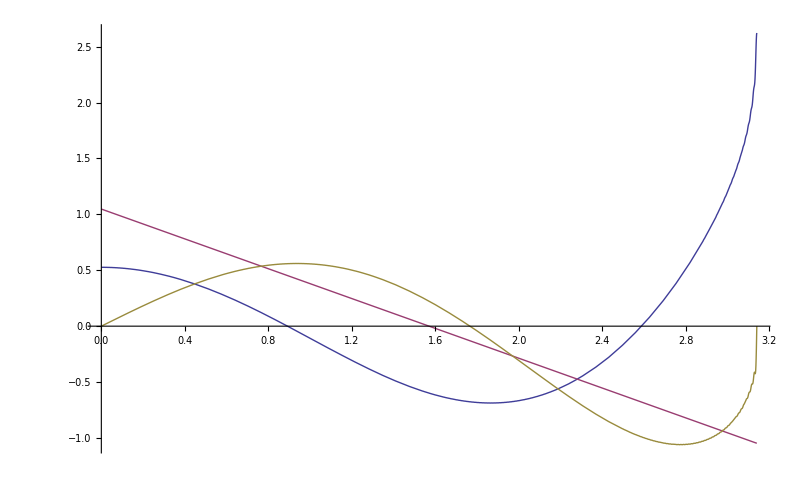

```mathematica
Plot[{∑_(n=2)^500 ((-1)^n/(n Log[n]))Cos[n x],(π-2x)/3,∑_(n=2)^500 ((-1)^n/(n Log[n]))Sin[n x]},{x,0,π},PlotRange->Full]
```

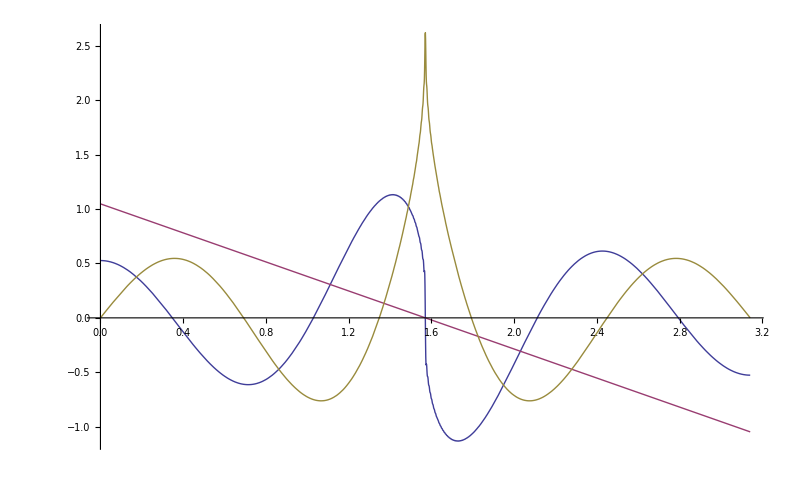

```mathematica
Plot[{∑_(n=2)^500 ((-1)^n/(n Log[n]))Cos[(2n+1)x],(π-2x)/3,∑_(n=2)^500 ((-1)^n/(n Log[n]))Sin[(2n+1)x]},{x,0,π}]
```

```mathematica
m=3;
While[m≤33,Print[Plot[∑_(n=100m)^(200m) ((-1)^n/(n Log[n]))Cos[(2n+1)x],{x,0,π},PlotRange->Full]];m++]
```

```mathematica
m=50;
Plot[∑_(n=100m)^(200m) ((-1)^n/(n Log[n]))Cos[(2n+1)x],{x,0,π},PlotRange->Full]
```